```mathematica
Clear["Global`*"]
```

```mathematica
survship=F0*Exp[(c0/c1)*(1-Exp[c1*t])];
```

```mathematica
F0=1;
a0=1.88*10^(-8.0);
b0=-0.56;
a1=1.45*10^(-7.0);
b1=-0.27;
c0=a0*M^b0;
c1=a1*M^b1;
```

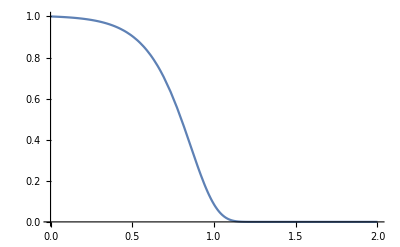

```mathematica
Plot[survship/.M->110031,{t,0,2000000000},PlotRange->{0,All}]
```

```mathematica
survder =D[ D[survship,t],t]
```

-c0 ⅇ^((c0 (1-ⅇ^(c1 t)))/c1+c1 t) (c1-c0 ⅇ^(c1 t)) F0

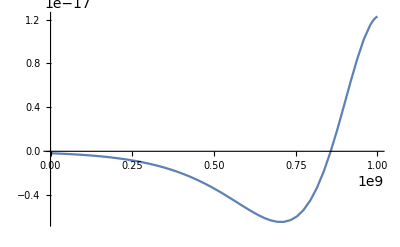

```mathematica
Plot[survder/.M->110031,{t,1,1000000000}]
```

```mathematica
Solve[survder==0,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→Log[c1/c0]/c1}}

```mathematica
NSolve[survship ==0.05,t]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{t→(1. Log[-(1. c1 (-(1. c0)/c1+Log[0.05/F0]))/c0])/c1}}

```mathematica
survhaldsat = D[survship]
```

```mathematica
bodylength==5.38674*mass^(0.32237);
```

```mathematica
Solve[bodylength==5.38674*mass^(0.32237),mass]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{mass→0.00538776 bodylength^3.10202562273164}}

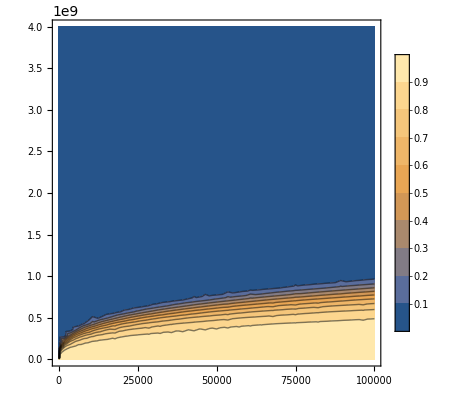

```mathematica
ContourPlot[survship,{M,1,100000},{t,0,4000000000},PlotRange->{0,All},PlotLegends->True]
```

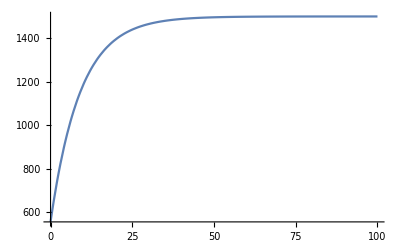

```mathematica
Plot[ Linf*(1-Exp[-k*(t-t0)])/.{k->0.11,t0->-4.2,Linf->1500},{t,0,100},PlotRange->All]
```

(Grams produced per gram per second) * (seconds/gram)

```mathematica
FullSimplify[(gramsoffspring/(gramsmom*seconds))*((gramsmom*seconds))]
```

gramsoffspring

```mathematica
Solve[W ==(5.388*10^(-6))*(PL^3.102),PL]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{PL→49.9394 W^0.322372662798195}}

```mathematica
grams*(1/grams)*grams^-0.15
```

1/grams^0.15

```mathematica
R0 * Exp[-(0.18*20)]
```

0.0273237 R0

```mathematica
avgfecundity =FullSimplify[Solve[Exp[-(M+r)] + lα*b*Exp[-r*α]*(1-Exp[-(M+r)*(w-α+1)])==1,b]]
```

{{b→(-1+ⅇ^(M+r))/((-ⅇ^(-(M+r) w+M α)+ⅇ^(M+r-r α)) lα)}}

```mathematica
Sship =FullSimplify[Solve[Exp[-(M+r)] + lα*b*Exp[-r*α]*(1-Exp[-(M+r)*(w-α+1)])==1,lα]]
```

{{lα→(-1+ⅇ^(M+r))/(b (-ⅇ^(-(M+r) w+M α)+ⅇ^(M+r-r α)))}}

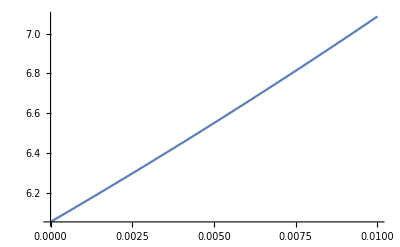

```mathematica
Plot[b/.(avgfecundity/.{M->2*0.15,w->30,lα->0.043,α->13}),{r,0,0.01},PlotRange->All]
```

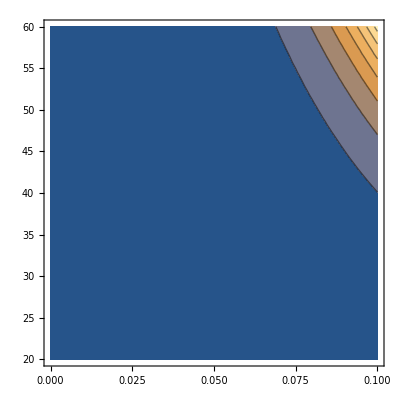

```mathematica
ContourPlot[b/.(avgfecundity/.{M->0.1,w->80,lα->0.1}),{r,0,0.1},{α,20,60},PlotRange->All]
```

```mathematica
survship=F0*Exp[(c0/c1)*(1-Exp[c1*t])];
```

```mathematica
Solve[b*Integrate[survship*Exp[-r*t],{t,t1,t2}]==1,b]
```

{{b→1/(∫_t1^t2 ⅇ^((c0 (1-ⅇ^(c1 t)))/c1-r t) F0ⅆt)}}

```mathematica
growthfunc = M*((1-(1-(m0/M)^(1-η))*Exp[(-a*(1-η)*t)/(M^(1-η))])^(1/(1-η)))
```

M (1-ⅇ^(-a M^(-1+η) t (1-η)) (1-(m0/M)^(1-η)))^(1/(1-η))

Body mass (grams) over time (seconds)

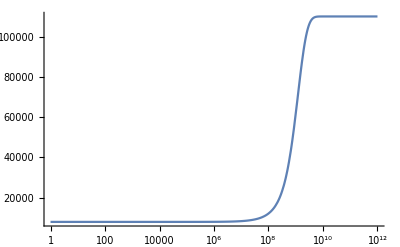

```mathematica
LogLinearPlot[growthfunc/.{m0->8000,M->110000,a->9.26*10^-8,η->3/4},{t,1,10^12},PlotRange->{5000,All}]
```

Mortality Rate (per year?) as a function of m(t)

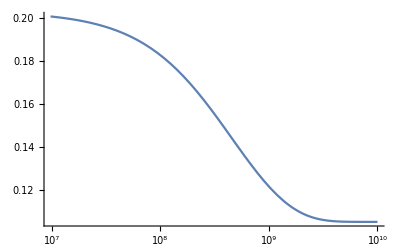

```mathematica
LogLinearPlot[(1.92m^-0.25/.m->growthfunc)/.{m0->8000,M->110000,a->9.26*10^-8,η->3/4},{t,0,10^10},PlotRange->{0,All}]
```

Survivorship from mortality rate

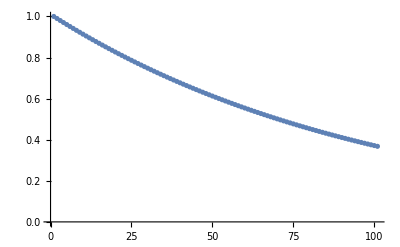

```mathematica
ListPlot[RecurrenceTable[{l[x] == l[x-1]*Exp[-0.01],l[0]==1},l,{x,0,100}],PlotRange->All]
```

```mathematica
Solve[FullSimplify[la*b*Sum[Exp[-M*(x-a)]*Exp[-r*x],{x,a,w}]]==1,la]
```

{{la→(ⅇ^(a r+(M+r) w) (-1+ⅇ^(M+r)))/(b (-ⅇ^(a M+a r)+ⅇ^(M+r+(M+r) w)))}}

```mathematica
survivorshiptox= Solve[FullSimplify[b*Sum[lx*Exp[-r*x],{x,a,w}]]==1,lx]
```

{{lx→(ⅇ^(a r+r w) (-1+ⅇ^r))/(b (-ⅇ^(a r)+ⅇ^(r+r w)))}}

```mathematica
(lx/.survivorshiptox)/.{w->30,a->13,b->9,r->0.032}
```

{0.0121147}

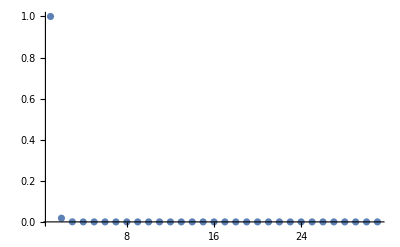

```mathematica
ListPlot[RecurrenceTable[{l[x] == l[x-1]*0.018,l[0]==1},l,{x,0,30}],PlotRange->All]
```

Sand tiger shark mortality: Z = 0.18 to 0.097 yr-1

```mathematica
0.097/(60*60*24*365)
```

3.07585×10^-9

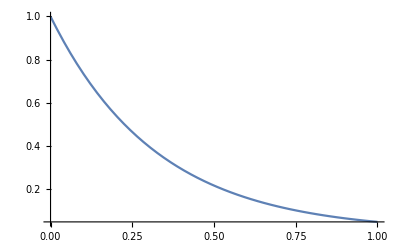

```mathematica
Plot[Exp[-t*Z]/.Z->3.075849822425165*^-9,{t,1,10^9},PlotRange->All]
```

Growth rate elasticity: 5.5% for fertility; 54.9% for juvenile survival; 59% for adult survival
Average fecundity: 
Leopard sharks: 6 female pups per female per year
Sandtiger sharks: 0.5 female pups per litter per year

Female pups per female per second

```mathematica
0.5/(60*60*24*365)
```

1.58549×10^-8

```mathematica
NSolve
```